#### BC_Chckerboard.nb: Calculate and display a matrix (checkerboard) of angles among elastic maps. INSTRUCTIONS: Run common_funs, ES_FindSymGroups, BC_ChooseTmat, BC_CumulativeBeta. The elastic map is specified in BC_CumulativeBeta.nb The notebook takes about 45 seconds to run.

```mathematica
ListSigmaOfΣn[Σn_]:=Join[Σn/@domain[Σn],ListComplement[ListSigmaAll,Σn/@domain[Σn]]]
```

```mathematica
ListSigmaOfΣn[ΣnTETXISO]
ListSigmaOfΣn[ΣnTETCUBE]
```

```mathematica
SigmaPairsMatrix[Σn_,dim_]:=Table[{Take[ListSigmaOfΣn[Σn],dim][[j]],Take[ListSigmaOfΣn[Σn],dim][[k]]},{j,dim},{k,dim}];
```

#### Example

```mathematica
MatrixForm[SigmaPairsMatrix[ΣnTETCUBE,6]]
```

#### Here is how the Map function works .

```mathematica
MatrixForm[Map[#[[1]]+#[[2]]&,SigmaPairsMatrix[ΣnTETCUBE,6],{2}]]
```

```mathematica
InternodalAngles[Tmat_,Σn_,nm_,dim_]:=Map[Round[AngleMatrix[SmatOfΣ[#[[1]],Tmat,Σn,nm],SmatOfΣ[#[[2]],Tmat,Σn,nm]]/Degree,.01]&,SigmaPairsMatrix[Σn,dim],{2}];
```

#### Example Choose node mode and node sequence (precomputed in BC_CumulativeBeta.nb)

```mathematica
nm=nm2; Σn=ΣnTETXISO;
MatrixNote[Tmat]
TextNodeMode[nm]
ListSigmaOfΣn[Σn]
MatrixForm[InternodalAngles[Tmat,Σn,nm,6]]
MatrixForm[InternodalAngles[Tmat,Σn,nm,8]]
```

```mathematica
rrow[i_,Tmat_,Σn_,nm_,dim_]:=Join[{Take[ListSigmaOfΣn[Σn],dim][[i]]},InternodalAngles[Tmat,Σn,nm,dim][[i]]];
rrow[0,Tmat_,Σn_,nm_,dim_]:=Join[{""},Take[ListSigmaOfΣn[Σn],dim]];
```

#### Example

```mathematica
Σn=ΣnTETCUBE;dim=8;
rrow[0,Tmat,Σn,nm2,dim]
rrow[3,Tmat,Σn,nm2,dim]
```

```mathematica
dim=6;WantNumbers="WantNumbers";
MatrixNote[Tmat]
TextNodeMode[nm]
MatrixForm[Table[rrow[i,Tmat,Σn,nm,dim],{i,0,dim}]]
```

```mathematica
gg[i_,j_,Tmat_,Σn_,nm_,dim_]:=InternodalAngles[Tmat,Σn,nm,dim][[i,j]];
```

#### Example

```mathematica
MatrixNote[Tmat]
TextNodeMode[nm]
gg[4,5,Tmat,ΣnTETXISO,nm,6]
```

```mathematica
Sort[Flatten[InternodalAngles[Tmat,Σn,nm,8]]]
```

```mathematica
ForScaling:=Max[Flatten[InternodalAngles[Tmat,ΣnTETXISO,nm2,8]]]; (* May need to change *)
```

```mathematica
ForScaling
```

```mathematica
PreCheckerboard[Tmat_,Σn_,nm_,dim_,ForScaling_,WantNumbers_]:={Table[{FaceForm[ColorData["TemperatureMap"][gg[i,j,Tmat,Σn,nm,dim]/ForScaling]],Cuboid[{i-.5,-j-.5},{i+.5,-j+.5}]},{i,dim},{j,dim}],
If[WantNumbers=="WantNumbers",Table[Text[Style[Round[gg[i,j,Tmat,Σn,nm,dim],.1],13],{i,-j}],{i,dim},{j,dim}]]};
```

```mathematica
hw=1.5;fontsize=15;WantRound="NoWantRound";increment=2;offset=2.5;
Show[legends[Range[0,24,4],22,SubscriptBox[Style["α",20],Style["MONO",11]]//DisplayForm,hw,fontsize,increment,offset],ImageSize->100,PlotRange->All]
```

```mathematica
Checkerboard[Tmat_,Σn_,nm_,dim_,ForScaling_,WantNumbers_,WantLegends_]:=Labeled[Graphics[{Text[#,{Position[Take[ListSigmaOfΣn[Σn],dim],#][[1,1]],0}]&/@Take[ListSigmaOfΣn[Σn],dim],Text[#,{-.2,-Position[Take[ListSigmaOfΣn[Σn],dim],#][[1,1]]}]&/@Take[ListSigmaOfΣn[Σn],dim],PreCheckerboard[Tmat,Σn,nm,dim,ForScaling,WantNumbers],If[WantLegends=="WantLegends",Inset[legends[Range[0,5+ForScaling,5],ForScaling,"",hww,fontsize,increment,offset],{3+dim,-3},Center,1.8]]},ImageSize->If[WantLegends=="WantLegends",510,350]],Style[SequenceForm[MatrixNote[Tmat],"  [",nm,"]"],14,FontFamily->"Arial"],{{Bottom,Left}} ]
```

```mathematica
nm=nm1;Σn=ΣnTETXISO;dim=6;WantNumbers="WantNumbers"
PreCheckerboard[Tmat,Σn,nm,dim,ForScaling,WantNumbers]
```

#### Examples

```mathematica
ForScaling
```

#### For legends. The setting increment = n prints every n^th contour label.

```mathematica
hww=1.2;fontsize=12;increment=1;offset=2.5; WantRound=="NoWantRound";
```

```mathematica
nm=nm1;Σn=ΣnTETXISO;dim=6;
MatrixNote[Tmat]
TextNodeMode[nm]
Checkerboard[Tmat,Σn,nm,dim,ForScaling,"NoWantNumbers","NoWantLegends"]
Checkerboard[Tmat,Σn,nm,dim,ForScaling,"NoWantNumbers","WantLegends"]
Print[" "];
```

```mathematica
TextNodeMode[nm1]
```

```mathematica
nm=nm2;Σn=ΣnTETCUBE;dim=8;
MatrixNote[Tmat]
Checkerboard[Tmat,Σn,nm,dim,ForScaling,"NoWantNumbers","NoWantLegends"]
Checkerboard[Tmat,Σn,nm,dim,ForScaling,"NoWantNumbers","WantLegends"]
Print[" "];
nm=nm3;Σn=ΣnTETXISO;dim=6;  (* dim must be nMax[Σn] for nm3 *)
MatrixNote[Tmat]
Checkerboard[Tmat,Σn,nm,dim,ForScaling,"WantNumbers","NoWantLegends"]
Checkerboard[Tmat,Σn,nm,dim,ForScaling,"WantNumbers","WantLegends"]
Print[" "];
```

```mathematica
dim=6;
Σn=ΣnTETXISO;
MatrixNote[Tmat]
Print[" UforNM1 = ", DispMat[UforNM1,2]];
Row[{Checkerboard[Tmat,ΣnTETXISO,nm1,dim,ForScaling,"WantNumbers","noWantLegends"],
Checkerboard[Tmat,ΣnTETXISO,nm2,dim,ForScaling,"WantNumbers","noWantLegends"],
Checkerboard[Tmat,ΣnTETXISO,nm3,dim,ForScaling,"WantNumbers","WantLegends"]}]
```

## For Reference (ΣnTETXISO only)

T is BrownAn00

UforNM1 = (0.92 | -0.37 | -0.12
-0.37 | -0.93 | 0.05
-0.13 | 0 | -0.99)

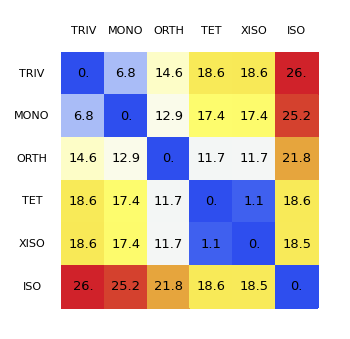
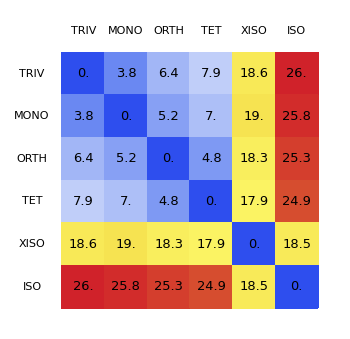
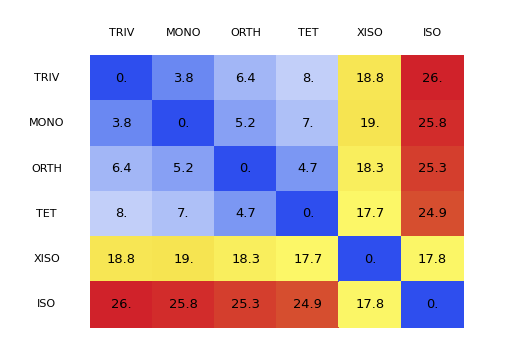
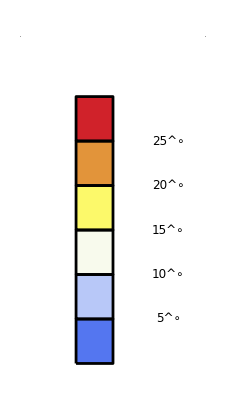
-Graphics-T is BrownAn00  [nm1]-Graphics-T is BrownAn00  [nm2]-Graphics-
-Graphics-T is BrownAn00  [nm3]